```mathematica
f[x_]=65-9.6 x^2+2.56 x^3;
```

```mathematica
um[x_]=If[x<2.5,f[x],f[2.5]];
τ = -1/1000;
c=100;
```

```mathematica
q=NDSolve[{u[x] D[u[x],x]-1/u[x] c[x]^2 D[u[x],x]==(um[x]-u[x])/τ,u[0]==15},{u[x]},{x,0,4.5}];
```

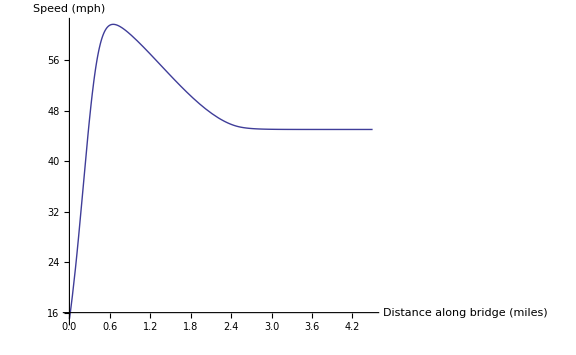

```mathematica
Plot[Evaluate[{u[x]}/.q],{x,0,4.5},{PlotRange->All,AxesLabel->{"Distance along bridge (miles)","Speed (mph)"},ImageSize->Large}]
```

```mathematica
60*NIntegrate[1/u[x]/.q,{x,0,4.5}]
```

{5.81144}